```mathematica
Oscillatore di Duffing
Metodi numerici per le equazioni differenziali
Giuseppe D'Auria
```

```mathematica
1.Soluzione numerica con Mathematica:
```

```mathematica
(*
Caso libero:
GAMMA=0;
	F=0;
	W=1;
	ALFA=1;*)

tmax:=10
sol= NDSolve[{v'[t]==k x[t] - ALFA x[t]^3 - GAMMA v[t] + F Cos[W t], x'[t]==v[t], x[0]==1, v[0]==1},{x,v},{t,0,tmax},MaxSteps->100 tmax];

sol2=sol//.{F->0,W->1,GAMMA->0,ALFA->1,k->1};

(* Con NDSolve senza metodo esplicito:
sol2= NDSolve[{v'[t]==x[t] - ALFA x[t]^3 - GAMMA v[t] + F Cos[W t], x'[t]==v[t], x[0]==1, v[0]==1},{x,v},{t,0,10}, MaxSteps-> 3500];*)

p1=Plot[x[t]/.sol2,{t,0,tmax},PlotStyle->Red,AxesLabel->{"t","x"},PlotLabel->"Posizioni x(t) Mathematica"];
p2=ParametricPlot[{x[t],v[t]}/.sol2,{t,0,tmax},PlotStyle->Red,AxesLabel->{"x","v"},PlotLabel->"Spazio delle fasi Mathematica"];
```

```mathematica
2.Soluzione numerica in C:
```

```mathematica
SetDirectory[];
SetDirectory["Desktop\\Esame Budinich"];
```

```mathematica
posizioni=Drop[Import["x(t).dat"],-1];
momenti=Drop[Import["p(x).dat"],-1];
p01=ListPlot[posizioni];
p02=ListPlot[momenti];

Show[p01,PlotLabel->"Posizioni x(t) in C, h=0.001",AxesLabel->{t,x[t]}];
Show[p02,PlotLabel->"Spazio delle fasi in C",AxesLabel->{x[t],p[t]}];
```

```mathematica
Show[p01,p1,AxesLabel->{"t","x"},PlotLabel->"Confronto posizioni x(t) C-Mathematica, h=0.001"]
Show[p02,p2,AxesLabel->{"x","v"},PlotLabel->"Spazio delle fasi C-Mathematica, h=0.001"]
```

```mathematica
3.Confronto tra la soluzione numerica in C e quella con Mathematica:
```

```mathematica
tempi=Table[n,{n,0,tmax-2/10,1/10}]; (*valori esatti per i tempi*)
Length[tempi]

xvaloriC=Transpose[posizioni][[2]];
xvaloriMat=x[tempi] /.sol2;
```

```mathematica
Length[xvaloriC];
FullForm[xvaloriC];
Length[valoriMat];
Length[valoriMat[[1]]];

Δ1=Abs[xvaloriMat[[1]]-xvaloriC];
Δ1s=xvaloriMat[[1]]-xvaloriC;

ListPlot[Transpose[{tempi,Δ1}],PlotLabel->"Δ1, h=0.001, 0≤t≤10 "]
ListPlot[Transpose[{tempi,Δ1s}],PlotLabel->"Δ1s, h=0.001, 0≤t≤10 "];


VvaloriC=Transpose[momenti][[2]];
VvaloriMat=x'[tempi] /.sol2;
Length[VvaloriMat];
Length[VvaloriMat[[1]]];

Δ2=Abs[VvaloriMat[[1]]-VvaloriC];
ListPlot[Transpose[{tempi,Δ2}],PlotLabel->"Δ2, h=0.001, 0≤t≤10 "]
```

```mathematica
4.Limiti di stabilità osservata dell'integrazione:
```

```mathematica
(*tmax:=100*)
```

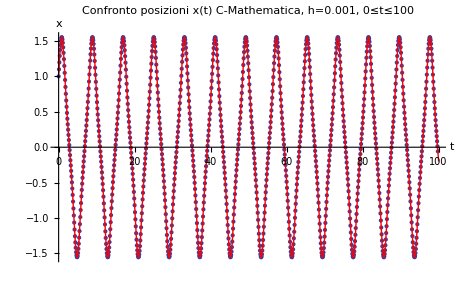

```mathematica
(*tmax:=500*)
```

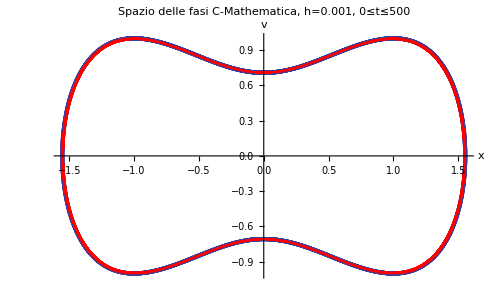

```mathematica
Prova con F=1, 0<t<20
```

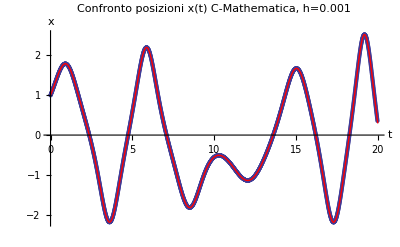

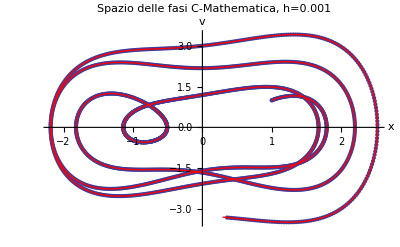

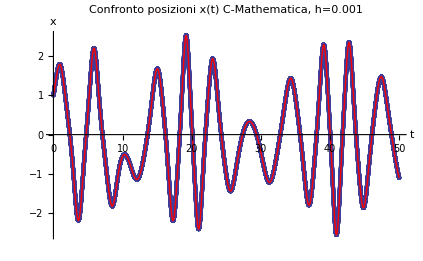

```mathematica
5.Caso fortemente caotico:
```

```mathematica
(* F=0.35, GAMMA=0.1,W=1.4,X0=0,V0=0, 0<t<100*)
```

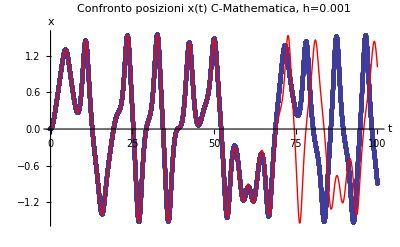

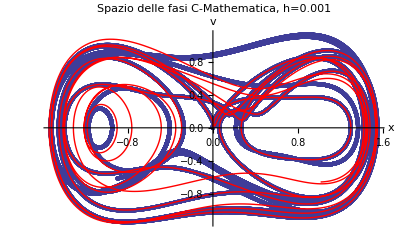

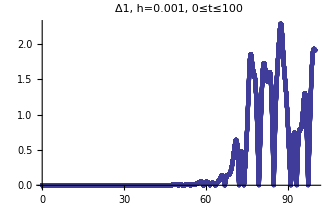

```mathematica
6.Studio dei vari regimi dinamici con Mathematica:

6.1. Caso non caotico con forzante
```

NDSolve::mxst: Maximum number of 3500 steps reached at the point t == 252.385.

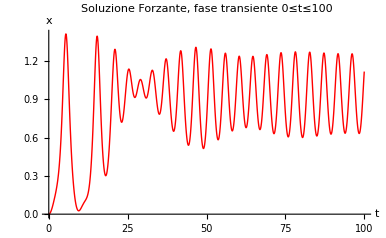

```mathematica
GAMMA=0.1;
F=0.1;
W=1.4;

sol4= NDSolve[{v'[t]==x[t] - x[t]^3 - GAMMA v[t] + F Cos[W t], x'[t]==v[t], x[0]==0 , v[0]==0},{x,v},{t,0,600}, MaxSteps-> 3500];
p8=Plot[x[t]/.sol4,{t,0,100},PlotStyle->Red,AxesLabel->{"t","x"},PlotLabel->"Soluzione Forzante, fase transiente 0≤t≤100"]
```

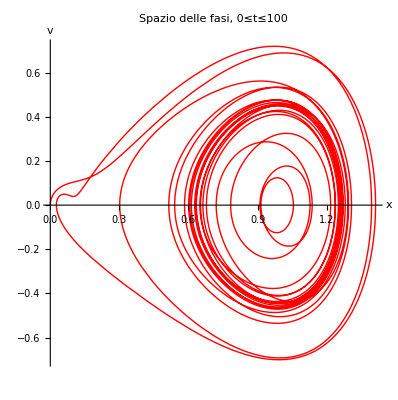

```mathematica
p9=ParametricPlot[{x[t],v[t]}/.sol4,{t,0,100},PlotStyle->Red,AxesLabel->{"x","v"},PlotLabel->"Spazio delle fasi, 0≤t≤100 "]
```

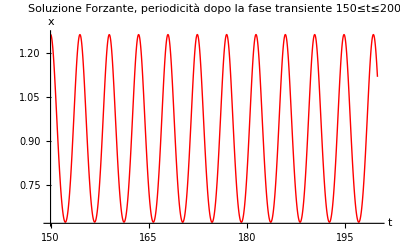

```mathematica
p10=Plot[x[t]/.sol4,{t,150,200},PlotStyle->Red,AxesLabel->{"t","x"},PlotLabel->"Soluzione Forzante, periodicità dopo la fase transiente 150≤t≤200"]
```

```mathematica
p11=ParametricPlot[{x[t],v[t]}/.sol4,{t,150,200},PlotStyle->Red,AxesLabel->{"x","v"},PlotLabel->"Spazio delle fasi dopo la fase transiente iniziale, 150≤t≤200 "]
```

```mathematica
Si osserva una semplice orbita periodica attorno al minimo del potenziale  x=1 (che è uno dei punti fissi trovati con considerazioni teoriche). 
Facendo alcune prove ho osservato che il periodo di questa orbita periodica è  T=2 PI/W  (come deve essere), con W la frequenza della forzante, cioè è circa T=4.48799. Ho cioè ritrovato tale valore  "sperimentalmente"integrando la soluzione per diversi periodi.
Ad esempio, nel grafico che segue ho integrato su un tempo di range=4.48 :si vede che l'orbita, per poco, non è completa.
```

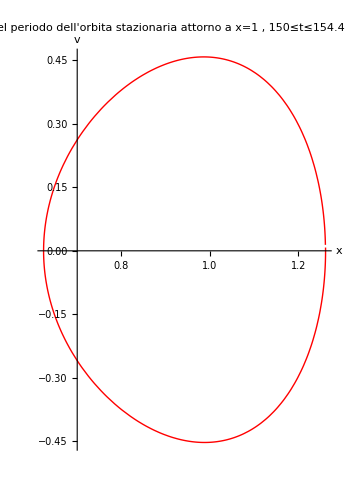

```mathematica
p12=ParametricPlot[{x[t],v[t]}/.sol4,{t,150,154.48},PlotStyle->Red,AxesLabel->{"x","v"},PlotLabel->"Stima del periodo dell'orbita stazionaria attorno a x=1 , 150≤t≤154.48 
Spazio fasi"]
```

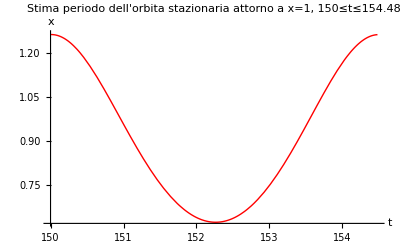

```mathematica
p13=Plot[x[t]/.sol4,{t,150,154.48},PlotStyle->Red,AxesLabel->{"t","x"},PlotLabel->"Stima periodo dell'orbita stazionaria attorno a x=1, 150≤t≤154.48"]
```

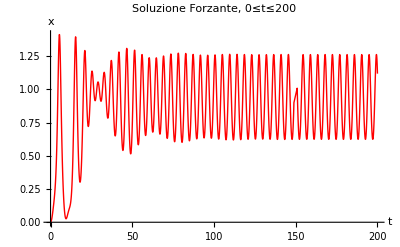

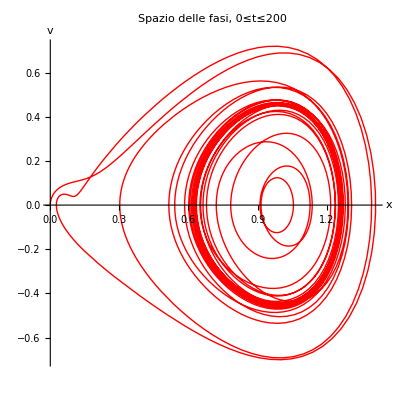

```mathematica
p14=Plot[x[t]/.sol4,{t,0,200},PlotStyle->Red,AxesLabel->{"t","x"},PlotLabel->"Soluzione Forzante,  0≤t≤200"]
p15=ParametricPlot[{x[t],v[t]}/.sol4,{t,0,200},PlotStyle->Red,AxesLabel->{"x","v"},PlotLabel->"Spazio delle fasi, 0≤t≤200 "]
```

```mathematica
Con queste condizioni iniziali,dopo la fase transiente, il sistema orbita stazionarmente attorno all'attrattore.
```

```mathematica
6.2. Caso caotico
```

```mathematica
Definisco, per comodità nei plot, le seguenti funzioni:
```

```mathematica
Clear["F"]
solution[F_, tmax_] := NDSolve[ {v'[t]== x[t] - x[t]^3 - GAMMA v[t] + F Cos[W t], x'[t]==v[t], x[0]==0, v[0]==0}, {x,v}, {t,0,tmax}, MaxSteps->100 tmax]
```

```mathematica
sol6=solution[F,tmax]//.{F->0.32,tmax->800}
```

NDSolve::ioppf: Value of option MaxSteps -> 100\ tmax should be a positive integer or Infinity.

{{x→InterpolatingFunction[{{0.,800.}},<>],v→InterpolatingFunction[{{0.,800.}},<>]}}

```mathematica
graphpos[tmin_,tmax_]:=Plot[x[t]/. sol6, {t,tmin,tmax},PlotStyle->Blue,AxesLabel->{"t","x"},PlotLabel->"Posizioni"] 
graphfasi[tmin_,tmax_]:=ParametricPlot[{x[t],v[t]}/. sol6, {t,tmin,tmax},PlotStyle->Blue,AxesLabel->{"x","v"},PlotLabel->"Spazio delle fasi"]
```

```mathematica
graphpos[0,200]
graphfasi[0,200]
```

```mathematica
Vediamo che la particella si muove da una parte all'altra delle buche di potenziale, tuttavia gran parte di questo moto complesso è ancora dovuto al transiente iniziale, come si può vedere dal comportamento ottenuto integrando per tempi successivi:
```

```mathematica
graphpos[750,800]
graphfasi[750,800]
```

```mathematica
Si noti come il periodo sia raddoppiato(T=4 Pi/W)Cioè la particella fa 2 giri attorno al minimo, con le condizioni iniziali scelte.
```

```mathematica
Ora incrementiamo ancora l'ampiezza forzante:
```

```mathematica
sol7=solution[0.338,2000]
```

{{x→InterpolatingFunction[{{0.,2000.}},<>],v→InterpolatingFunction[{{0.,2000.}},<>]}}

```mathematica
graphpos[1600,2000]
graphfasi[1600,2000]
```

```mathematica
graphpos[0,2000]
```

```mathematica
graphfasi[0,2000]
```

```mathematica
Nota:vi sono segni di ergodicità.
```

```mathematica
7.Mappe di Poincarè in Mathematica:
```

```mathematica
Per semplificarmi la vita, definisco una volta per tutte una funzione ,"poincare", che produce una sezione di Poincarè per dati valori F, GAMMA e W,ottenuta  allargando lo spazio delle fasi con theta che è ciclica e intersecando ricorsivamente lo spazio con piani a periodi costanti.
```

```mathematica
poincare[F_,GAMMA_,W_,ntagliati_,nplot_,spessorepunti_]:= (T=2 Pi/W; g[{xold_,vold_}]:={x[T],v[T]}
/.NDSolve[{v'[t]==x[t]-x[t]^3-GAMMA v[t]+F Cos[ W t],x'[t]== v[t],x[0]== xold,v[0]== vold},{x,v},{t,0,T}][[1]];
lp=ListPlot[Drop[NestList[g,{0,0},nplot+ntagliati],ntagliati],PlotStyle ->{PointSize[spessorepunti],Hue[0]},PlotRange -> All,AxesLabel ->{"x","v"}])
```

```mathematica
Posso fare anche un filmino:
```

```mathematica
ListAnimate[Table[poincare[n,0.1,1.4,200,2000,0.008],{n,0.34,0.35,0.001}]]
```

```mathematica
poincare[0.49,0.1,1.4,0,2000,0.008]
```

```mathematica
poincare[0.567,0.1,1.4,0,2000,0.008]
```

```mathematica
poincare[0.570,0.1,1.4,200,2000,0.008]
```

```mathematica
poincare[0.1,0.3,1.4,200,2000,0.008]
```

```mathematica
8.Dimostro che è un frattale:
```

```mathematica
poincare[0.35,0.1,1.4,200,15000,0.002]
```

```mathematica
Plotto un riquadro per selezionare la zona che voglio ingrandire per verificare se veramente è una figura invariante per scala.
```

```mathematica
Show[lp,Epilog ->{GrayLevel[0.6],Thickness[0.006],Line[{{0.8,0.35},{0.8,0.67},{1.05,0.67},{1.05,0.35},{0.8,0.35}}]}]
```

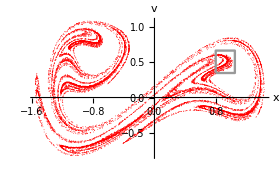

```mathematica
Modifico leggermente la funzione poancare per plottare nel range che scelgo:
```

```mathematica
poincare2[F_,GAMMA_,W_,ntagliati_,nplot_,spessorepunti_,xmin_,xmax_,vmin_,vmax_]:=(T=2 Pi/W;g[{xold_,vold_}]:={x[T],v[T]}/.NDSolve[{v'[t]==x[t]-x[t]^3-GAMMA v[t]+F Cos[W t],x'[t]==v[t],x[0]==xold,v[0]==vold},{x,v},{t,0,T}][[1]];
lp2=ListPlot[Drop[NestList[g,{0,0},nplot+ntagliati],ntagliati],PlotRange ->{{xmin,xmax},{vmin,vmax}},PlotStyle ->{PointSize[spessorepunti],Hue[0]},PlotRange->All,AxesLabel->{"x","v"},AxesOrigin ->{xmin,vmin},AspectRatio ->1])
```

```mathematica
poincare2[0.35,0.1,1.4,2000,100000,0.003,0.8,1.05,0.35,0.67];
```

```mathematica
Show[lp2,Epilog ->{GrayLevel[0.6],Thickness[0.006],Line[{{0.86,0.48},{0.91,0.48},{0.91,0.58},{0.86,0.58},{0.86,0.48}}]}]
```

```mathematica
poincare2[0.35,0.1,1.4,2000,1000000,0.005,0.86,0.91,0.48,0.58];
```

```mathematica
Show[lp2,Epilog ->{GrayLevel[0.6],Thickness[0.006],Line[{{0.88,0.525},{0.88,0.55},{0.888,0.55},{0.888,0.525},{0.88,0.525}}]}]
```

```mathematica
Effettivamente si osserva una struttura autosimilare ad ogni ingrandimento, caratteristico dei frattali. Nota:per plottare abbastanza finemente questo grafico ci sono voluti 10^6 punti e mezz'ora di tempo di calcolo!
```

```mathematica
9.Lyapunov:
```

```mathematica
posizNP=Drop[Import["x(t)nonpert.dat"],-1];
fasiNP=Drop[Import["p(x)nonpert.dat"],-1];
p101=ListPlot[posizNP,PlotStyle->Blue];
p102=ListPlot[fasiNP,PlotStyle->Blue];

posizP=Drop[Import["x(t)pert.dat"],-1];
fasiP=Drop[Import["p(x)pert.dat"],-1];
p101P=ListPlot[posizP,PlotStyle->Orange,];
p102P=ListPlot[fasiP,PlotStyle->Orange];

Show[p101,PlotLabel->"Posizioni non perturbate x(t) in C, h=0.001"];
Show[p102,PlotLabel->"Spazio delle fasi non perturbato in C"];

Show[p101P,PlotLabel->"Posizioni perturbate x(t) in C, h=0.001"];
Show[p102P,PlotLabel->"Spazio delle fasi perturbato in C"];

Show[p102,p102P,PlotLabel->"Spazi delle fasi perturbato e non perturbato sovrapposti"]


lx=ListPlot[Log[   Abs[  Transpose[posizP][[2]] -  Transpose[posizNP][[2]]  ]],PlotStyle->Blue,PlotLabel->"posizioni, δx=10^(-7) 
x[0]=0 , v[0]=0
xp[0]=0+δx , vp[0]=0
"]
lv=ListPlot[Log[   Abs[  Transpose[fasiP][[2]] -  Transpose[fasiNP][[2]]  ]],PlotStyle->Green,PlotLabel->"momenti, δx=10^(-7)
x[0]=0 , v[0]=0
xp[0]=0+δx , vp[0]=0
"]
```

```mathematica
8.Prova con forza impulsiva in C:
```

```mathematica
L'idea è di inserire una forza impulsiva ad un certo istante di tempo per vedere come  reagisce il sistema per diverse condizioni sui vari parametri.
```

```mathematica
posizdelta=Drop[Import["x(t)delta.dat"],-1];
momedelta=Drop[Import["p(x)delta.dat"],-1];
pimp1=ListPlot[posizdelta];
pimp2=ListPlot[momedelta];

Show[pimp1,PlotLabel->"Posizioni con Forza impulsiva in C, TD=50, FD=10.0 h=0.001",AxesLabel->{t,x[t]}]
Show[pimp2,PlotLabel->"Spazio delle fasi con Forza impulsiva in C, TD=50, FD=10.0 h=0.001",AxesLabel->{x[t],p[t]}]
```

```mathematica
Regime caotico (F=0.35,W=1.4,GAMMA=0.1) con Delta di Dirac in t=50.
```

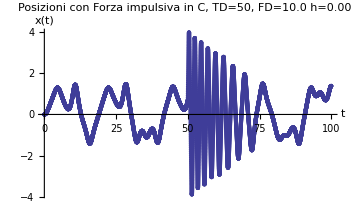

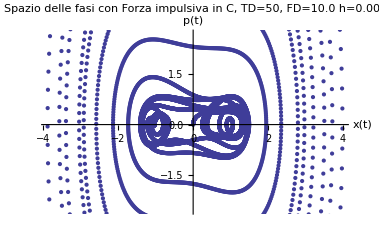

```mathematica
Caso libero (F=0,W=1,GAMMA=0) con Delta di Dirac in t=50.
```

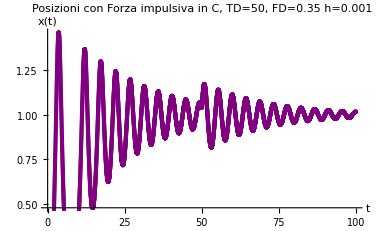
```mathematica
(F=0,W=1.4,GAMMA=0.1,X0=-1,V0=1) con Delta di Dirac in t=50.


-Graphics-
```

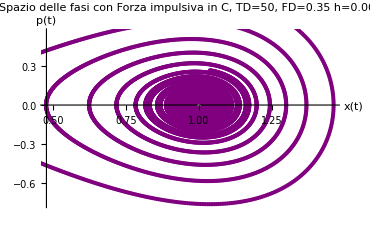

```mathematica
(F=0,W=1.4,GAMMA=0.1,X0=-4,V0=1) con Delta di Dirac in t=50.
```

```mathematica
Plottando la soluzione senza Forza impulsiva nelle stesse condizioni, si cambia attrattore finale.
```